```mathematica
WeightedAdjacencyMatrix[GridGraph[{8,8}]]//MatrixForm
```

```mathematica
V = IdentityMatrix[64]
```

```mathematica
Zeq[nmax_]:=PseudoInverse[Module[{eta = -ⅈ*0.000001,Minput,Q,Q2},Minput=WeightedAdjacencyMatrix[GridGraph[{nmax,nmax}]];
Q:=Module[{X=Minput},Do[X[[j,j]]=Sum[X[[j,jp]],{jp,1,nmax}]-eta,{j,1,nmax*nmax}];X];(*Q2:=Module[{MI=PseudoInverse[Q]},MI⟦1,1⟧+MI⟦nmax*nmax,nmax*nmax⟧-MI⟦1,nmax*nmax⟧-MI⟦nmax*nmax,1⟧];*)
Q]]
```

```mathematica
g[nmax_,h_]:=g[nmax,h]=Module[{J= Zeq[nmax]},
Do[J=PseudoInverse[IdentityMatrix[nmax*nmax]-J.V.J.V].J,{loc1,h}];
J]
```

```mathematica
R[nmax_,h_]:= Module[{abc=g[nmax,h]},abc[[1,1]]+abc[[nmax*nmax,nmax*nmax]]-abc[[1,nmax*nmax]]-abc[[nmax*nmax,1]]]
```

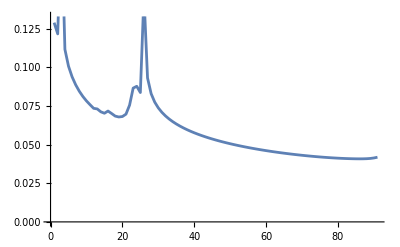

```mathematica
Monitor[Table[R[8,h]//Abs,{h,100,1000,10}],h]//ListLinePlot
```

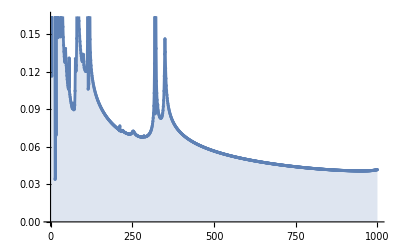

```mathematica
ListPlot[%25,Filling->Axis,Mesh->All,Joined->True]
```